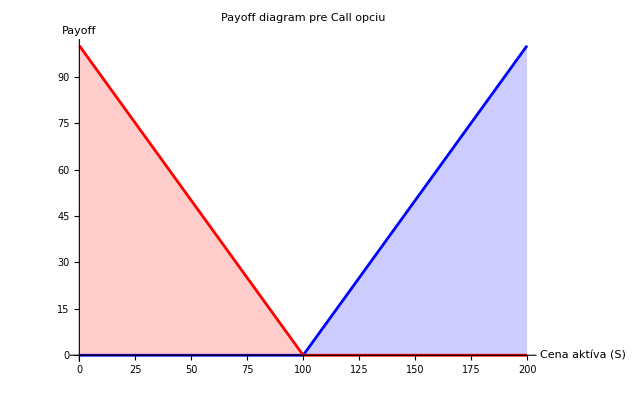

```mathematica
(*2.1*)
K=100; (*Expiračná cena*)
Smax=200; 

callPayoff[S_]:=Max[0,S-K]
putPayoff[S_]:=Max[0,K-S]

(*Vytvorenie dát pre grafy*)
S=Range[0,Smax,1];
callValues=callPayoff/@S;
putValues=putPayoff/@S;

Show[Plot[callPayoff[S],{S,0,Smax},PlotRange->All,AxesLabel->{"Cena aktíva (S)","Payoff"},PlotLabel->"Payoff diagram pre Call opciu",Filling->Axis,PlotStyle->Blue],
Plot[putPayoff[S],{S,0,Smax},PlotRange->All,AxesLabel->{"Cena aktíva (S)","Payoff"},PlotLabel->"Payoff diagram pre Put opciu",Filling->Axis,PlotStyle->Red]]
```

```mathematica
(*2.2*)
```

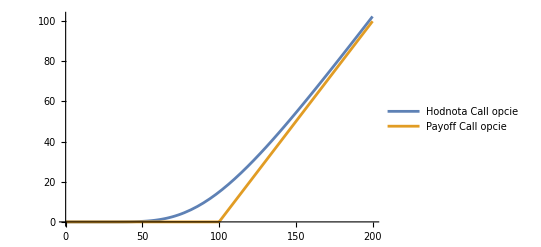

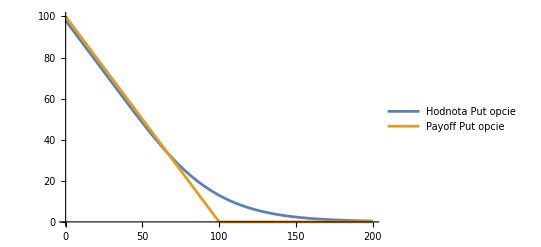

```mathematica
s=Smax;      (*aktuálna cena podkladového aktíva*)
e=K;     (*expiračná cena*)
Sigma=0.5; (*volatilita*)
r=0.04;    (*spojitá úroková miera*)
tau=0.5;   (*čas do expirácie*)
d=0;       (*dividenda*)
(*Funkcie pre d1 a d2*)
d1[S_]:=(Log[S/e]+(r-d+(Sigma^2)/2)*tau)/(Sigma*Sqrt[tau]);
d2[S_]:=d1[S]-Sigma*Sqrt[tau];
(*Funkcie pre hodnotu call a put opcie*)
CallValue[S_]:=S*Exp[-d*tau]*CDF[NormalDistribution[],d1[S]]-e*Exp[-r*tau]*CDF[NormalDistribution[],d2[S]]//N;
PutValue[S_]:=e*Exp[-r*tau]*CDF[NormalDistribution[],-d2[S]]-S*Exp[-d*tau]*CDF[NormalDistribution[],-d1[S]]//N;
Plot[{CallValue[t],callPayoff[t]},{t,0,Smax}, PlotLegends->{"Hodnota Call opcie","Payoff Call opcie"}]
Plot[{PutValue[t],putPayoff[t]},{t,0,Smax}, PlotLegends->{"Hodnota Put opcie","Payoff Put opcie"}]
```

```mathematica
(*2.3*)
```

```mathematica
e=90; (*Expiračná cena*)
r=0.04; (*Úroková miera*)
sigma=0.2; (*Volatilita*)
Smax=100; (*Maximálna cena akcie*)
Tmax=1; (*Maximálny expiračný čas*)

putSolution=NDSolve[{D[V[S,t],t]+(1/2)*sigma^2*S^2*D[V[S,t],{S,2}]+r*S*D[V[S,t],S]-r*V[S,t]==0,V[S,0]==Max[0,e-S],(*Počiatočná podmienka pre put opciu*)V[0,t]==0,(*Okrajová podmienka pre S=0*)V[Smax,t]==e*Exp[-r*(Tmax-t)]-Smax  (*Okrajová podmienka pre Smax*)},V,{S,0,Smax},{t,0,Tmax}];
```

NDSolve::mxsst: Using maximum number of grid points 10000 allowed by the MaxPoints or MinStepSize options for independent variable S.

NDSolve::ibcinc: Warning: boundary and initial conditions are inconsistent.